```mathematica
ClearAll["Global`*"];
```

```mathematica
coords = {t,r,θ,ϕ};
n=Length[coords];
rplus = M+Sqrt[M^2-a^2];
tt=2 M r/ρ-1;
rr=ρ/Δ;
θθ=ρ;
ϕϕ=(Δ+(2 M r (r^2+a^2))/ρ) Sin[θ]^2;
tϕ=-2 a M r Sin[θ]^2/ρ;
metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm;
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm;
Rtor[R_]:=R-a^2/RH;
```

```mathematica
a=.;M=.;
ρ=r^2+a^2 Cos[θ]^2;
Δ=r^2 - 2 M r+ a^2;christoffel :=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
geodesic :=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
```

```mathematica
riemann:=riemann=Simplify[Table[D[christoffel[[i,j,l]],coords[[k]]]-D[christoffel[[i,j,k]],coords[[l]]]+Sum[christoffel[[s,j,l]] christoffel[[i,k,s]]-christoffel[[s,j,k]]christoffel[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}];
```

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]]
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

{}

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]] ricci[[i,j]],{i,1,n},{j,1,n}]]
```

0

```mathematica
einstein:=einstein=Simplify[ricci-(1/2) scalar*metric]
listeinstein:=Table[If[UnsameQ[einstein[[j,l]],0],{ToString[G[j,l]],einstein[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listeinstein],Null],2],TableSpacing->{2,2}]
```

{}

```mathematica
(* the solver function. It takes in the max τ, the initial velocities in r,θ,ϕ and the initial coordinates in t,r,θ,ϕ. *)
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
τend = maxτi;
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,
{τ,0,maxτi},
Method->{"EventLocator","Event":>(r[τ]≤1.01*RH),"EventAction":>Throw[τend=τ,"StopIntegration"]}
];
soln]
(* this next function translates from spherical coordinates to Cartesian coordinates to make plotting simpler *)
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=r[τ] Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=r[τ] Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=r[τ] Cos[θ[τ]]/.soln;{xs,ys,zs}]
(* This one calculates u dot u *)
udotu[solni_,τval_]:=Block[{xα,uα},xα=Table[coords[[i]][τ]/.solni,{i,1,n}]//Flatten; uα=D[xα,τ];
xα=xα/.τ->τval;uα=uα/.τ->τval;uα.((metric/.Table[coords[[i]]->xα[[i]],{i,1,n}]).uα)]
(* And this one prints out the coordinates *)
coordlist[τin_,soln_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

```mathematica
genXYPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},soln=computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τend},AxesLabel->{x,y},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},soln=computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{x,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},soln=computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[2]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},soln=computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot3D[Evaluate[Re[xyz]//Flatten],{τ,0,τend},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
```

```mathematica
τend=.;uinvar = 0;
rh=1.0;ct=-0.05;
M=(rh-2ct)/2.0
a = Sqrt[ct(ct-rh)](rh-2ct)/2/M
RH = M+Sqrt[M^2-a^2];
(* Since we are plotting in the BL space, the horizon is at RH, not rh *)
horizpl=PolarPlot[RH,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=100;
```

0.55

0.229129

```mathematica
soln=computeSoln[τPlot,{-0.1,0,0.01},{0,8 RH,π/2,0}];
xyzsoln=sphslnToCartsln[soln];
Table[{τi,Rtor[coords[[2]][τ]/.soln/.τ->τi]},{τi,0,100,1}]
```

{{0,{8.35}},{1,{8.25034}},{2,{8.15139}},{3,{8.05316}},{4,{7.95569}},{5,{7.85899}},{6,{7.76309}},{7,{7.66802}},{8,{7.57382}},{9,{7.4805}},{10,{7.3881}},{11,{7.29665}},{12,{7.20619}},{13,{7.11674}},{14,{7.02835}},{15,{6.94104}},{16,{6.85487}},{17,{6.76985}},{18,{6.68605}},{19,{6.60348}},{20,{6.52221}},{21,{6.44227}},{22,{6.36371}},{23,{6.28656}},{24,{6.21089}},{25,{6.13674}},{26,{6.06415}},{27,{5.99318}},{28,{5.92388}},{29,{5.85629}},{30,{5.79048}},{31,{5.7265}},{32,{5.6644}},{33,{5.60423}},{34,{5.54605}},{35,{5.48992}},{36,{5.43588}},{37,{5.384}},{38,{5.33433}},{39,{5.28692}},{40,{5.24182}},{41,{5.19909}},{42,{5.15877}},{43,{5.12092}},{44,{5.08558}},{45,{5.0528}},{46,{5.02261}},{47,{4.99507}},{48,{4.9702}},{49,{4.94804}},{50,{4.92863}},{51,{4.91198}},{52,{4.89812}},{53,{4.88708}},{54,{4.87887}},{55,{4.87349}},{56,{4.87097}},{57,{4.8713}},{58,{4.87448}},{59,{4.88051}},{60,{4.88937}},{61,{4.90107}},{62,{4.91557}},{63,{4.93285}},{64,{4.9529}},{65,{4.97569}},{66,{5.00118}},{67,{5.02933}},{68,{5.06012}},{69,{5.0935}},{70,{5.12942}},{71,{5.16784}},{72,{5.20872}},{73,{5.252}},{74,{5.29763}},{75,{5.34557}},{76,{5.39576}},{77,{5.44814}},{78,{5.50266}},{79,{5.55927}},{80,{5.61791}},{81,{5.67853}},{82,{5.74107}},{83,{5.80548}},{84,{5.87171}},{85,{5.93969}},{86,{6.00938}},{87,{6.08073}},{88,{6.15368}},{89,{6.22819}},{90,{6.30421}},{91,{6.38168}},{92,{6.46057}},{93,{6.54082}},{94,{6.62239}},{95,{6.70524}},{96,{6.78933}},{97,{6.87462}},{98,{6.96106}},{99,{7.04862}},{100,{7.13726}}}

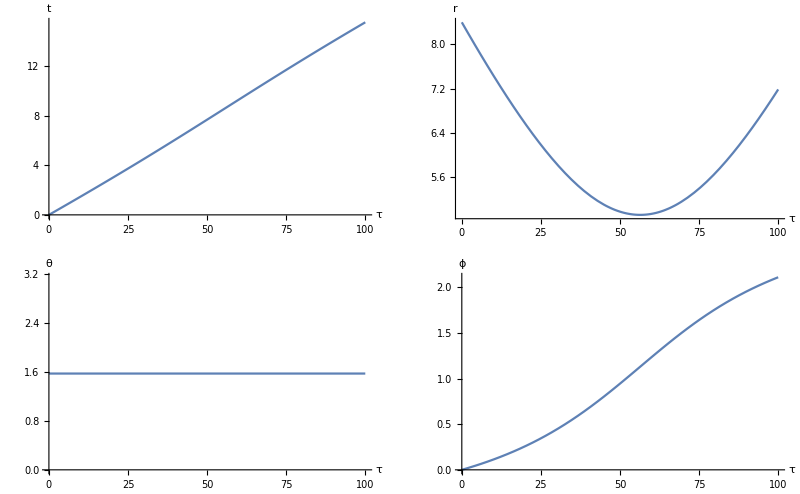

```mathematica
GraphicsGrid[{{Plot[{Evaluate[coords[[1]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","t"}],Plot[{Evaluate[coords[[2]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","r"}]},{Plot[{Evaluate[coords[[3]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","θ"}],Plot[{Evaluate[coords[[4]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","ϕ"}]}}]
```

For initial coordinates={0,4.2,π/2,0} and initial velocities={-0.1,0,0.01} the particle crosses the horizon at τend=35.5528

With final coordinates={t = 11.0122,r = 1.0605,θ = 1.5708,ϕ = 2.34225}

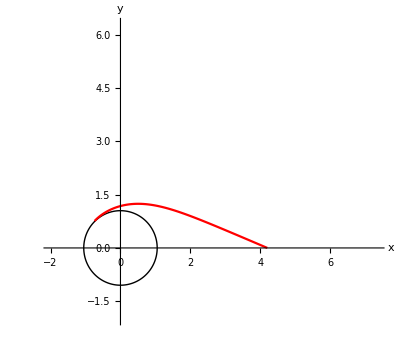

```mathematica
(* first one, in red, is other Kerr and the second one, in blue, is BL Kerr *)
genXYPlot[τPlot,{0,4 RH,π/2,0},{-0.1,0,0.01},1];
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-2,7RH},{-2,6RH}}]
```

```mathematica
(* BL coords *)
Print["a=",a,", M=",M,", rh=",rh,", ct=",ct]
r0=50;
NumberForm[tt/.r->r0/.θ->π/2,16];
NumberForm[rr/.r->r0/.θ->π/2,16];
NumberForm[θθ/.r->r0/.θ->π/2,16];
NumberForm[ϕϕ/.r->r0/.θ->π/2,16];
NumberForm[tϕ/.r->r0/.θ->π/2,16];
NumberForm[christoffel[[1,1,2]]/.r->r0/.θ->π/2,16]
NumberForm[christoffel[[2,2,2]]/.r->r0/.θ->π/2,16]
NumberForm[christoffel[[1,1,1]]/.r->r0/.θ->π/2,16]
NumberForm[christoffel[[3,2,2]]/.r->r0/.θ->π/2,16]
```

a=0.229129, M=0.55, rh=1., ct=-0.05

0.0002249487689937128

-0.0002245146065370785

0

0.